{n2→(u-x^2)/(u+x)}

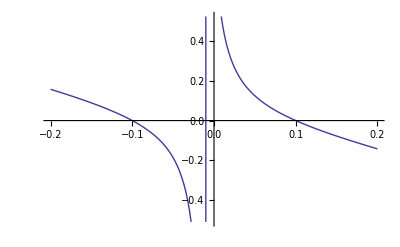

```mathematica
Eps=({{(u+x)/(u-1), ⅈ*(√u(1+x))/(u-1), 0}, {-ⅈ*(√u(1+x))/(u-1), (u+x)/(u-1), 0}, {0, 0, -x}});
ξ=({{ξx}, {ξy}, {0}});
Solve[FullSimplify[FullSimplify[Det[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})((ξᵀ.ξ)[[1]][[1]])-ξ.ξᵀ-ξ0^2*Eps]]/.{ξx^2+ξy^2->ξ0^2*n2,-ξx^2-ξy^2->ξ0^2*n2}]==0,n2][[2]]
Plot[n2/.%/.u->0.01,{x,-0.2,0.2}]
```

```mathematica
eq1=Ey'[x]-ⅈ*χ(B[x]+Sin[θ]*Ex[x]);
eq2=Sin[θ]*B[x]+(Eps[[1]][[1]]*Ex[x]+Eps[[1]][[2]]*Ey[x]);
eq3=B'[x]-ⅈ*χ(Eps[[2]][[1]]*Ex[x]+Eps[[2]][[2]]*Ey[x]);

(*Equation for Ex[x]*)
eq1/.Solve[eq2==0,B[x]];
D[eq2,x]/.Solve[eq3==0,B'[x]];
D[eq1,x]/.Solve[eq3==0,B'[x]];
D[%%,x]/.Solve[%==0,Ey''[x]];
%/.Solve[{%%%==0,%%%%==0},{Ey[x],Ey'[x]}];
eq=FullSimplify[%[[1]][[1]][[1]]] ;

A1=FullSimplify[(eq/.{Ex[x]->0,Ex'[x]->0})/Ex''[x]]
A2=FullSimplify[(eq/.{Ex[x]->0,Ex''[x]->0})/Ex'[x]]
A3=FullSimplify[(eq/.{Ex'[x]->0,Ex''[x]->0})/Ex[x]]
```

(u+x)/(-1+u)

(2 √u-2 u (1+x) χ Csc[θ]+(u+x) χ Sin[θ])/(u (1+x)^2 χ Csc[θ]+(-1+u) (√u+(u+x) χ Sin[θ]))

(χ ((-1+u) √u (3 u+x-2 x^2) χ+u (-2+2 u+(1+x)^2 (u-x^2) χ^2) Csc[θ]+Sin[θ] (1-u^2+(u+x) (u^2+x^2-2 u (1+x+x^2)) χ^2-(-1+u) (u+x) χ Sin[θ] (2 √u+(u+x) χ Sin[θ]))))/((-1+u) (u (1+x)^2 χ Csc[θ]+(-1+u) (√u+(u+x) χ Sin[θ])))

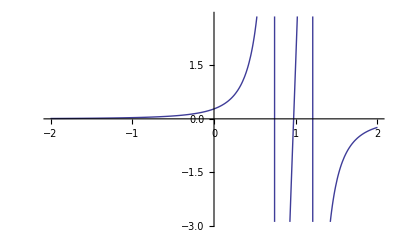

```mathematica
α=π*0.064;
valsPlus={θ->α,χ->30,u->0.01};
valsMinus={θ->-α,χ->30,u->0.01};
Plot[((A2/A1)/.valsPlus)-((A2/A1)/.valsMinus),{x,-2,2}]
```